# Root Finding with Bisection and Newton’s Method

## The Basic Bisection Routine

### Bisection Module

It takes, as inputs, a function F (the function whose roots we are interested in), an initial bracketing, (that is, a pair x and x) and a tolerance ϵ that specified how close to zero the function should be before the module exits.

### Simple Test

F(x) = x - πx - 2x + 5

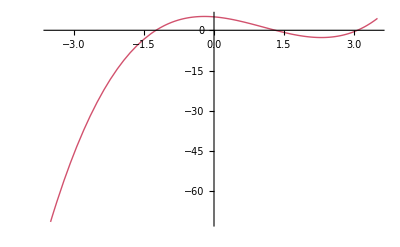

-1.2415

1.31093

3.07216

```mathematica
(*Define the function with respect to x*)
F[x_]:=(x^3)-(Pi*x^2)-(Sqrt[2]*x)+5;
RecursiveBisect[F_,x1_,xr_,eps_]:=Module[{val,vam,xm,retval},
xm=.5(x1+xr); (*average the starting position with the second position*)
val = F[x1];(*left initial*)
vam=F[xm];(*right initial*)
If[Abs[vam]≤eps,(*check to see that the value is less than the tolerance*)
Return[xm];
];
If[val vam <0,(*pos*pos = pos && neg*neg = pos, so have to find when there is a negative and a positive value*)
retval=RecursiveBisect[F,x1,xm,eps];
,
retval=RecursiveBisect[F,xm,xr,eps];
];
Return[retval];
]
Plot[F[x],{x,-3.5,3.5},PlotStyle->Thick,ColorFunction->Function[{x},ColorData["NeonColors"][x]]]
RecursiveBisect[F,-3,-1,.00000001]
RecursiveBisect[F,0,2.4,.00000001]
RecursiveBisect[F,2.5,4,.00000001]
```

## Bisection Variant (Franklin 3.11)

### Initial Bracket Module

The inputs should be the function F, and an initial value x and step size δ.  The code should begin by looking at the region [x, x + δ], and checking whether or not there is a root in it.  If there isn’t, it should look at the region  [x, x - δ].  Then it should look at the region  [x + δ, x + 2δ], and then [x - δ, x - 2δ], and so on, until it finds a bracketing with a root in it.  The module should then output a pair of values, {x, x}, based on this.

### Testing the bracket module

F(x) = x - πx - 2x + 5

with the initial values -1, 1, and 3.  Take steps of size 0.1.  Confirm that your results are consistent with what you found earlier.

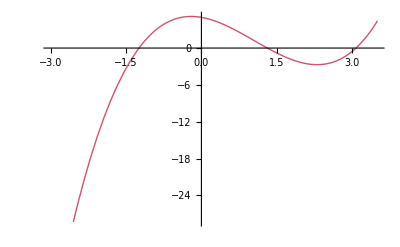

The bracket is:{1.2,1.4}

1.3

The bracket is:{-1.4,-1.2}

-1.3

The bracket is:{3.,3.2}

3.1

```mathematica
F[x_]:=(x^3)-(Pi*x^2)-(Sqrt[2]*x)+5;
BisectV[F_,x0_,S_]:=Module[{xl,L,xr,R,N,avg},
(*Initialize left and right change in x*)
xl =x0-S;
xr=x0+S;
L =F[xl];
R=F[xr];
(*need to change distance of bracket so that signs flip. The counter is denoted by N.  This is what is described as the number multiplied by the step size.  To get it to switch directions each time, have to use (-1)^N because even N values will be positive, so go to the right, and odd N values will be negative so to the left.  Then, L and R can be initialized as the brackets once the function stops iterating. *)
For[N=1, R* L > 0, N++;xl=xl+((-1)^N)*S*N; xr=xr+((-1)^N)*S*N;
L=F[xl];
R=F[xr];
];
avg=(xl+xr)*.5;
Print["The bracket is:",{xl,xr}];
Return[avg]
]
Plot[F[x],{x,-3,3.5},PlotStyle->Thick,ColorFunction->Function[{x},ColorData["NeonColors"][x]]]
BisectV[F,1,.1]
BisectV[F,-10,.1]
BisectV[F,10,.1]
(*Can get more precision with a smaller S*)
```

### Combining modules

A module that combines both the bracket finder and the bisection routine, taking as inputs the function F, initial point x, step size δ, and tolerance ϵ.

```mathematica
F[x_]:=(x^3)-(Pi*x^2)-(Sqrt[2]*x)+5;
BisectCombo[F_,x0_,S_,eps_]:=Module[{xl,L,xr,R,N,a,b,avg,xm,x1,val,vam,retval},
xl =x0-S;
xr=x0+S;
L =F[xl];
R=F[xr];
For[N=1, R  L > 0, N++;
xl=xl+((-1)^N)*S*N;
xr=xr+((-1)^N)*S*N;
L =F[xl];
R=F[xr];
];
a= xl;
b=xr;
Print["The bracket is:",{a,b}];
xm=.5(a+b);
val=F[a];
vam=F[xm];
(*If tolerance is smaller than the average distance between the brackets, then it will return the average between the brackets.  Otherwise, it will return the zero at step size S (delta)*)
If[Abs[vam]≥   eps,
Return[xm],Return[a]
];
]
BisectCombo[F,-1,.00001,.000001]
BisectCombo[F,1,.00001,.000001]
BisectCombo[F,4,.00001,.000001]
```

The bracket is:{-1.2415,-1.24148}

-1.24149

The bracket is:{1.31092,1.31094}

1.31093

The bracket is:{3.07216,3.07218}

3.07217

```mathematica
(*This method is in agreement with the bracket finder and the bisection routine*)
```

## Basic Newton’s Method

A module that takes as its inputs a function F, an initial value x, and a tolerance ϵ, and uses Newton’s method to find a root.  Use a numerical approximation to find the derivative of F:

F’[x] = F[x + δ] - F[x]

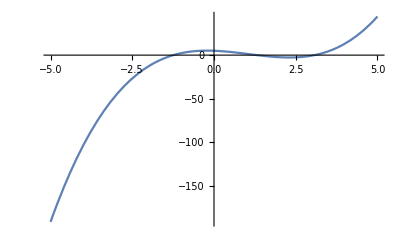

-1.2415

1.31093

3.07216

```mathematica
F[x_]:=(x^3)-(Pi*x^2)-(Sqrt[2]*x)+5;
DF[x_]:= (3*x^2)-(2*Pi*x)-Sqrt[2];
Newton[F_,delta_,x0_,eps_]:=Module[{x,deltax,val,DF},
DF[x_]:=(F[x+delta]-F[x-delta])/(2.delta);
x=x0;
val=F[x];
While[Abs[val]≥eps,
deltax=-F[x]/DF[x];
x=x+deltax;
val=F[x];
];
Return[x];
]

Plot[F[x],{x,-5,5}]
Newton[F,.001,-3,.00001]
Newton[F,.001,1,.00001]
Newton[F,.001,4,.00001]
```

```mathematica
(*In agreement with the bisection modules*)
```

## Comparing Newton’s Method and Bisection (Franklin 3.12)

F(x) = sin(x - 2x - 1)

Find the root that lies in the region [0, 3], with an initial estimate x = 2, using tolerance ϵ = 10.

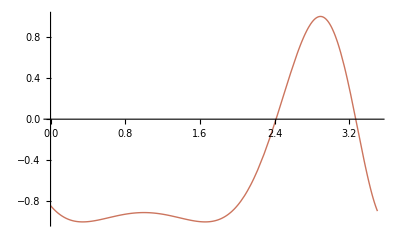

7

2.41421

```mathematica
(*First I use Newton's method and find the number of iterations.  Then in the next module, I use a bracketing bisection and find the number of iterations.  Both answers are in agreement with each other, but the bracketing method has a much larger number of iterations compared to Newton's method.  I have the tolerance set to 10^-6 because 10^-8 takes too long.  At 10^6, it already has 828,424 iterations. It may be more beneficial to use Newton if time constraints are an issue*)
F[x_]:=Sin[(x^2)-(2*x)-1];
DF[x_]:= Cos[(x^2)-(2*x)-1]*((2x)-2);
NewtonwithN[F_,delta_,x0_,eps_]:=Module[{x,deltax,val,DF,N,xi},
DF[x_]:=(F[x+delta]-F[x-delta])/(2.delta);
x=x0;
val=F[x];
N=1;
While[Abs[val]≥eps,
deltax=-F[x]/DF[x];
N++;
x=x+deltax;
val=F[x];
];
Print[N];
Return[x];
]
Plot[F[x],{x,0,3.5},PlotStyle->Thick,ColorFunction->Function[{x},ColorData["NeonColors"][x]]]
NewtonwithN[F,.0000001,2,10^-8]
```

```mathematica
F[x_]:=Sin[(x^2)-(2*x)-1];
BisectV[F_,x0_,S_]:=Module[{xl,L,xr,R,N,avg},
xl =x0-S;
xr=x0+S;
L =F[xl];
R=F[xr];
(*N is the iterator*)
For[N=1, R* L > 0, N++;xl=xl+((-1)^N)*S*N; xr=xr+((-1)^N)*S*N;
L=F[xl];
R=F[xr];
];
avg=(xl+xr)*.5;
Print["The bracket is:",{xl,xr}];
Print["The number of iterations is: ",N];
Return[avg]
]
Plot[F[x],{x,0,3.5},PlotStyle->Thick,ColorFunction->Function[{x},ColorData["NeonColors"][x]]]
BisectV[F,2,.000001]
```

-Graphics-

The bracket is:{2.41421,2.41421}

The number of iterations is: 828424

2.41421

## Problem 3.13

```mathematica
In this problem, W vector is given as Rsin(omega t)xhat + Rcos(omega t) yhat + vt zhat.  The distance R is 2 meters and omega is 10 hertz.  The velocity is one-tenth of the speed of light.  Additionally the r vector is given by a length of one in each cartesian direction.  In this problem I am asked to find the location of the moving charge at the location of r.  I did this using Newton's method to find the root.
```

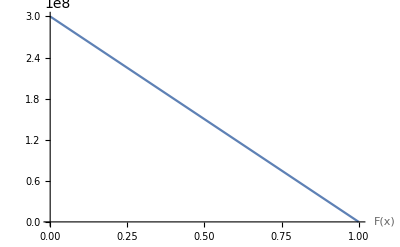

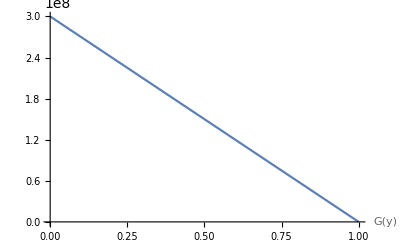

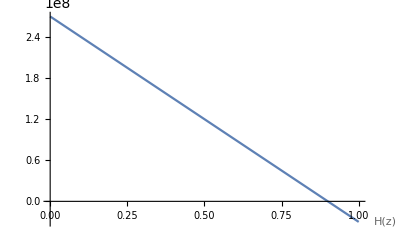

```mathematica
F[x_]:=3*10^8*(1-x)-Abs[1-2*Sin[10*1]];
G[y_]:=3*10^8*(1-y)-Abs[1-2*Cos[10*1]];
H[z_]:=3*10^8*(1-z)-Abs[.1*3*10^8*1];
Plot[F[x],{x,0,1},PlotLabels->"Expressions"]
Plot[G[y],{y,0,1},PlotLabels->"Expressions"]
Plot[H[z],{z,0,1},PlotLabels->"Expressions"]
```

```mathematica
F[x_]:=3*10^8*(1-x)-Abs[1-2*Sin[10*1]];
DF[x_]:=-3*10^8;
RTimeF[F_,delta_,x0_,eps_]:=Module[{x,deltax,val,DF},
DF[x_]:=(F[x+delta]-F[x-delta])/(2.delta);
x=x0;
val=F[x];
While[Abs[val]≥eps,
deltax=-F[x]/DF[x];
x=x+deltax;
val=F[x];
];
Return[x];
]
(*This is not surprising since Sin[10] is extremely small relative to the speed of light*)
RTimeF[F,.000000001,0.1,10^-7]
```

1.

```mathematica
G[y_]:=3*10^8*(1-y)-Abs[1-2*Cos[10*1]];
DG[y_]:=-3*10^8;
RTimeG[G_,delta_,y0_,eps_]:=Module[{y,deltax,val,DG},
DG[y_]:=(G[y+delta]-G[y-delta])/(2.delta);
y=y0;
val=G[y];
While[Abs[val]≥eps,
deltax=-G[y]/DG[y];
y=y+deltax;
val=G[y];
];
Return[y];
]
(*This is not surprising since Cos[10] is extremely small relative to the speed of light*)
RTimeG[G,.00000001,0.1,10^-7]
```

1.

```mathematica
H[z_]:=3*10^8*(1-z)-Abs[.1*3*10^8*1];
DH[z_]:=-3*10^8;
RTimeH[H_,delta_,z0_,eps_]:=Module[{z,deltax,val,DH},
DH[z_]:=(H[z+delta]-H[z-delta])/(2.delta);
z=z0;
val=H[z];
While[Abs[val]≥eps,
deltax=-H[z]/DH[z];
z=z+deltax;
val=H[z];
];
Return[z];
]
(*In this, there is actually a change in the root.  Since the zhat direction of W is related to the particles velocity, there is actually a difference in location*)
RTimeH[H,.0000001,0.1,10^-7]
```

0.9

## Problem 3.15

```mathematica
In this problem, I am asked to find the angle of an arbitrary height function using given perameters.  For F[x] the initial velocity is 100 m/s.
```

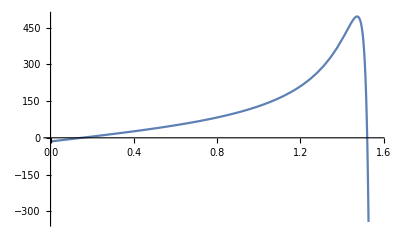

0.148992

```mathematica
F[x_]:=100 * Tan[x]-(4.9*(100^2/(100^2*Cos[x]*Cos[x])))-((10000)/1000);
Kinematics[F_,x1_,xr_,eps_]:=Module[{val,vam,xm,retval},
xm=.5(x1+xr);
val = F[x1];
vam=F[xm];
If[Abs[vam]≤eps,
Return[xm];
];
If[val vam <0,
retval=Kinematics[F,x1,xm,eps];
,
retval=Kinematics[F,xm,xr,eps];
];
Return[retval];
]
Plot[F[x],{x,0, Pi/2}]
Kinematics[F,0,.5,10^-5]
```

```mathematica
(* Then,I am asked to test what happens when the velocity is 10 m/s.  I redo the function below, but change the v to 10 from 100.*)
```

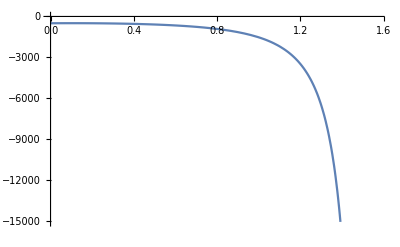

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 100 Tan[0.5].

retval$1273

```mathematica
F[x_]:=100 * Tan[x]-(4.9*(100^2/(10^2*Cos[x]*Cos[x])))-((10000)/1000);
Kinematics[F_,x1_,xr_,eps_]:=Module[{val,vam,xm,retval},
xm=.5(x1+xr);
val = F[x1];
vam=F[xm];
If[Abs[vam]≤eps,
Return[xm];
];
If[val vam <0,
retval=Kinematics[F,x1,xm,eps];
,
retval=Kinematics[F,xm,xr,eps];
];
Return[retval];
]
Plot[F[x],{x,0, Pi/2}]
Kinematics[F,0,.5,10^-5]
```

```mathematica
(*As you can see at ten m/s , the object does not have a great enough initial velocity to make it all the way.  This explains why there is an error, as well as why it just goes down to negative infinity.*)
```